Data file Importing:

```mathematica
AppendTo[$Path,"Desktop/PhotonInterferenceLab/Analysis"];
AppendTo[$Path,"/Users/emulder/GitHub/PhotonInterferenceLab/Analysis"];
AppendTo[$Path,"/Users/iliparti/PhotonInterferenceLab/Analysis"];
data2Slit = Import["4.45mmAll.csv"];
dataFarSlit = Import["4mmAll.csv"];
dataNearSlit = Import["5.9mmAll.csv"];
data2SlitAvg = Import["4.45mmAvg.csv"];
dataFarSlitAvg = Import["4mmAvg.csv"];
dataNearSlitAvg = Import["5.9mmAvg.csv"];
data2SlitErr = Import["4.45mmError.csv"];
dataFarSlitErr = Import["4mmError.csv"];
dataNearSlitErr = Import["5.9mmError.csv"];
dataDouble=Import["just_values_double.csv"];
dataNear=Import["just_values_near.csv"];
dataFar=Import["just_values_far.csv"];
```

```mathematica
Needs["ErrorBarPlots`"]
```

Fraunhofer Model for double slit and single slit: fit comparison with data and parameter optimization

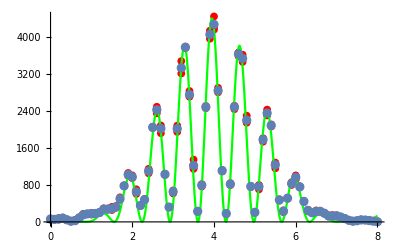

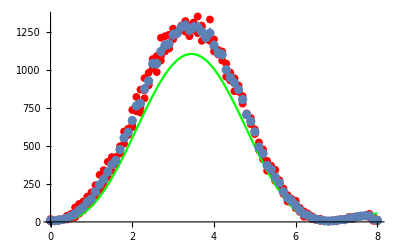

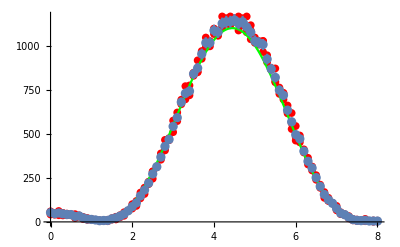

```mathematica
g[x_]:= I0*((Sin[Pi*a*Sin[(x-x0)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x0)/D2])))^2)*(Cos[Pi*d*Sin[(x-x0)/D2]/lambda]^2)+c;
I0 = 4400;
a = 0.085;
d = 0.406;
lambda = 0.000555;
x0 = 3.95;
c = 3.6;
D1=338;
D2=500;
fit = Plot[g[x],{x,0,8},PlotStyle->Green];
dataPlot2Slit =ListPlot[data2Slit,PlotMarkers->{Automatic,8},PlotStyle->Red];
dataPlot2SlitAvg=ErrorListPlot[Table[{data2SlitAvg[[i]],ErrorBar[.01,Flatten[data2SlitErr][[i]]]},{i,81}]];
Show[dataPlot2Slit,fit,dataPlot2SlitAvg]

h[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x1)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x1)/D2])))^2)+c;
x1 = 3.45;
fit2 = Plot[h[x],{x,0,8},PlotRange->All,PlotStyle->Green];
dataPlotFarSlit = ListPlot[dataFarSlit,PlotMarkers->{Automatic,8},PlotStyle->Red];
dataPlotFarSlitAvg=ErrorListPlot[Table[{dataFarSlitAvg[[i]],ErrorBar[.01,Flatten[dataFarSlitErr][[i]]]},{i,81}]];
Show[dataPlotFarSlit,fit2,dataPlotFarSlitAvg]

k[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x2)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x2)/D2])))^2)+c;
x2 = 4.45;
fit3 = Plot[k[x],{x,0,8},PlotRange->All,PlotStyle->Green];
dataPlotNearSlit = ListPlot[dataNearSlit,PlotMarkers->{Automatic,8},PlotStyle->Red];
dataPlotNearSlitAvg = ErrorListPlot[Table[{dataNearSlitAvg[[i]],ErrorBar[.01,Flatten[dataNearSlitErr][[i]]]},{i,81}]];
Show[dataPlotNearSlit,fit3,dataPlotNearSlitAvg]
```

Fresnel Model for double slit and single slit: fit comparison with data and parameter optimization

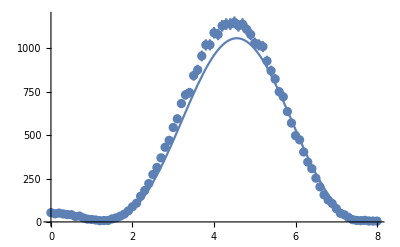

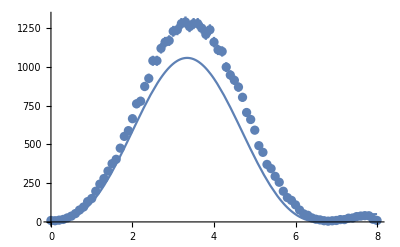

```mathematica
slit1[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0+(d/2),x0+(d/2)+a}]
s1[z_]:=33.3*I0*Re[slit1[z]*Conjugate[slit1[z]]]
slit2[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0-(d/2)-a,x0-(d/2)}]
s2[z_]:=33.3*I0*Re[slit2[z]*Conjugate[slit2[z]]]
fitb=Plot[s1[z],{z,0,8},PlotRange->All];
fitc=Plot[s2[z],{z,0,8},PlotRange->All];
Show[fitb,dataPlotNearSlitAvg]
Show[fitc,dataPlotFarSlitAvg]
```

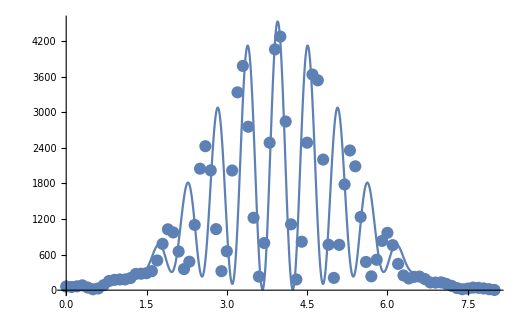

```mathematica
slitdouble[z_]:=slit1[z]+slit2[z]
slit[z_]:=40*I0*Re[slitdouble[z]*Conjugate[slitdouble[z]]]
fita=Plot[slit[z],{z,0,8}];
Show[fita,dataPlot2SlitAvg]
```

Data Analysis Fresnel and Fraunhofer ALL

```mathematica
pearsonTest[obs_List,exp_List]/;Length[obs]==Length[exp]:=Block[{t},t=Total[(obs-exp)^2/exp]//N;
{Rule["chisqr",t],Rule["p-val",SurvivalFunction[ChiSquareDistribution[Length[exp]-1],t]]}]
chisq[data_,dist_]:=Total[Table[(data[[u]]-dist[[u]])^2/dist[[u]],{u,0,Length[data],1}]];
```

```mathematica
dataTable2Slit=Flatten[Table[{Flatten[dataDouble]⟦u+1⟧},{u,0,80,1}]];
dataTableNearSlit=Flatten[Table[{Flatten[dataNear]⟦u+1⟧},{u,0,80,1}]];
dataTableFarSlit=Flatten[Table[{Flatten[dataFar]⟦u+1⟧},{u,0,80,1}]];
```

```mathematica
dist2SlitFres=Flatten[Table[{slit[u/10]},{u,0,80,1}]];
distNearSlitFres=Flatten[Table[{s1[u/10]},{u,0,80,1}]];
distFarSlitFres=Flatten[Table[{s2[u/10]},{u,0,80,1}]];
```

```mathematica
dist2SlitFraun=Flatten[Table[{g[u/10]},{u,0,80,1}]];
distNearSlitFraun=Flatten[Table[{k[u/10]},{u,0,80,1}]];
distFarSlitFraun=Flatten[Table[{h[u/10]},{u,0,80,1}]];
```

```mathematica
DistributionFitTest[dataTable2Slit,dist2SlitFres]
```

0.923242

```mathematica
pearsonTest[dataTable2Slit,dist2SlitFres]
```

{chisqr→148650.,p-val→6.74924586132356×10^-32136}

```mathematica
chisq[dataTable2Slit,dist2SlitFres]
chisq[dataTableFarSlit,distFarSlitFres]
chisq[dataTableNearSlit,distNearSlitFres]
chisq[dataTable2Slit,dist2SlitFraun]
chisq[dataTableFarSlit,distFarSlitFraun]
chisq[dataTableNearSlit,distNearSlitFraun]
```

148650.

4836.27

1289.81

52621.6

1607.48

136.601

Data Analysis Fresnel and Fraunhofer JUST THE PART WITH INTERFERENCE

```mathematica
dataTable2SlitPart=Flatten[Table[{Flatten[dataDouble]⟦u+1⟧},{u,20,60,1}]];
dataTableNearSlitPart=Flatten[Table[{Flatten[dataNear]⟦u+1⟧},{u,20,60,1}]];
dataTableFarSlitPart=Flatten[Table[{Flatten[dataFar]⟦u+1⟧},{u,20,60,1}]];
```

```mathematica
dist2SlitFresPart=Flatten[Table[{slit[u/10]},{u,20,60,1}]];
distNearSlitFresPart=Flatten[Table[{s1[u/10]},{u,20,60,1}]];
distFarSlitFresPart=Flatten[Table[{s2[u/10]},{u,20,60,1}]];
```

```mathematica
dist2SlitFraunPart=Flatten[Table[{g[u/10]},{u,20,60,1}]];
distNearSlitFraunPart=Flatten[Table[{k[u/10]},{u,20,60,1}]];
distFarSlitFraunPart=Flatten[Table[{h[u/10]},{u,20,60,1}]];
```

```mathematica
chisq[dataTable2SlitPart,dist2SlitFresPart]
chisq[dataTableFarSlitPart,distFarSlitFresPart]
chisq[dataTableNearSlitPart,distNearSlitFresPart]
chisq[dataTable2SlitPart,dist2SlitFraunPart]
chisq[dataTableFarSlitPart,distFarSlitFraunPart]
chisq[dataTableNearSlitPart,distNearSlitFraunPart]
```

146556.

2132.52

305.6

15727.8

982.605

67.7862